```mathematica
Subscript[x, 0]=-7;Subscript[x, 1]=-4;Subscript[x, 2]=0;Subscript[x, 3]=5;
Subscript[f, 0]= 32;Subscript[f, 1]=-24;Subscript[f, 2]=5;Subscript[f, 3]=85;
n=3;
Subscript[P, k_][X_]=Subscript[f, k]+ (X-Subscript[x, k])(Subscript[A, k] X^2+Subscript[B, k] X+Subscript[C, k]);
eg8=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
eg9={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
Subscript[PP, k_][X_]=D[Subscript[P, k][X], X];
eg10=Table[Subscript[PP, k][Subscript[x, k+1]]==Subscript[PP, k+1][Subscript[x, k+1]],{k,0,n-2}];
eg11={Subscript[PP, n-1][Subscript[x, n]]==0};
Subscript[PPP, k_][X_]=D[Subscript[PP, k][X], X];
eg12=Table[Subscript[PPP, k][Subscript[x, k+1]]==Subscript[PPP, k+1][Subscript[x, k+1]],{k,0,n-2}];
eg13={Subscript[PPP, 0][Subscript[x, 0]]==0};
eg14=Join[eg8,eg9,eg10,eg11,eg12,eg13];
koef=Solve[eg14,{}]//Flatten
Spl[X_]=Table[Subscript[P, k][X]/.koef,{k,0,n-1}]//Expand
```

{A_0→8033/14472,A_1→-1631/6432,A_2→-10357/20100,B_0→56231/7236,B_1→4771/1608,B_2→785/402,C_0→6397/1809,C_1→29/4,C_2→15371/804}

{102667/1809+(139735 X)/2412+(56231 X^2)/4824+(8033 X^3)/14472,5+(15371 X)/804+(785 X^2)/402-(1631 X^3)/6432,5+(15371 X)/804+(785 X^2)/402-(10357 X^3)/20100}

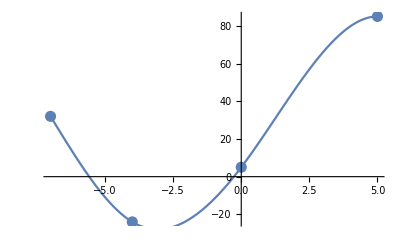

```mathematica
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}];
Gr5= ListPlot[Tb1,PlotStyle->{PointSize[0.02]}];
Gr6=Table[Plot[Spl[X][[k]],{X,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
Show[Gr5,Gr6]
```